```mathematica
ClearAll[Evaluate[Context[]<>"*"]]
```

```mathematica
eqns={x^2/a^2+y^2/b^2==1,y==k x+m};
polyex=Apply[Subtract,eqns,{1}];
polys=Numerator[Together[Apply[Subtract,eqns,{1}]]];
xpoly=Collect[Resultant[polys[[1]],polys[[2]],y],x]
discx=Factor[Discriminant[xpoly,x]]   (*discriminant*)
frist=Solve[eqns,{x,y}]//FullSimplify;
{{x1,y1},{x2,y2}}={x,y}/.frist;
second={x1+x2,x1 x2,y1+y2,y1 y2}//FullSimplify
thrid={x1 x2+y1 y2,x1 y2+x2 y1}//FullSimplify
slope=-CoefficientList[polyex[[2]],x][[2]];    (*k*)
intercept=-CoefficientList[CoefficientList[polyex[[2]],y][[1]],x][[1]] ;  (*m*)
Chordlength=FullSimplify[Sqrt[1+slope^2] Sqrt[(x1+x2)^2-4 x1 x2]]    (*AbsAB*)
```

-a^2 b^2+a^2 m^2+2 a^2 k m x+(b^2+a^2 k^2) x^2

4 a^2 b^2 (b^2+a^2 k^2-m^2)

{-(2 a^2 k m)/(b^2+a^2 k^2),(a^2 (-b^2+m^2))/(b^2+a^2 k^2),(2 b^2 m)/(b^2+a^2 k^2),(b^2 (-a^2 k^2+m^2))/(b^2+a^2 k^2)}

{(-a^2 b^2 (1+k^2)+(a^2+b^2) m^2)/(b^2+a^2 k^2),-(2 a^2 b^2 k)/(b^2+a^2 k^2)}

2 √(1+k^2) √((a^2 b^2 (b^2+a^2 k^2-m^2))/((b^2+a^2 k^2)^2))

```mathematica
ClearAll[Evaluate[Context[]<>"*"]]
eqns={x^2/a^2+y^2/b^2==1,x==t y+n};
polyex=Apply[Subtract,eqns,{1}];
polys=Numerator[Together[Apply[Subtract,eqns,{1}]]];
xpoly=Collect[Resultant[polys[[1]],polys[[2]],x],y]
discx=Factor[Discriminant[xpoly,y]]   (*discriminant*)
frist=Solve[eqns,{x,y}]//FullSimplify;
{{x1,y1},{x2,y2}}={x,y}/.frist;
second={x1+x2,x1 x2,y1+y2,y1 y2}//FullSimplify
thrid={x1 x2+y1 y2,x1 y2+x2 y1}//FullSimplify
slope=-CoefficientList[polyex[[2]],y][[2]];    (*k*)
intercept=-CoefficientList[CoefficientList[polyex[[2]],y][[1]],x][[1]] ;  (*m*)
Chordlength=FullSimplify[Sqrt[1+slope^2] Sqrt[(y1+y2)^2-4 y1 y2]]    (*AbsAB*)
```

-a^2 b^2+b^2 n^2+2 b^2 n t y+(a^2+b^2 t^2) y^2

4 a^2 b^2 (a^2-n^2+b^2 t^2)

{(2 a^2 n)/(a^2+b^2 t^2),(a^2 (n-b t) (n+b t))/(a^2+b^2 t^2),-(2 b^2 n t)/(a^2+b^2 t^2),(b^2 (-a^2+n^2))/(a^2+b^2 t^2)}

{(a^2 n^2+b^2 n^2-a^2 b^2 (1+t^2))/(a^2+b^2 t^2),-(2 a^2 b^2 t)/(a^2+b^2 t^2)}

2 √(1+t^2) √((a^2 b^2 (a^2-n^2+b^2 t^2))/((a^2+b^2 t^2)^2))

```mathematica
ClearAll[Evaluate[Context[]<>"*"]]
eqns={x^2/a^2+y^2/b^2==1,y==k (x-x0)+y0};
polyex=Apply[Subtract,eqns,{1}];
polys=Numerator[Together[Apply[Subtract,eqns,{1}]]];
xpoly=Collect[Resultant[polys[[1]],polys[[2]],y],x]
discx=Factor[Discriminant[xpoly,x]]   (*discriminant*)
frist=Solve[eqns,{x,y}]//FullSimplify;
{{x1,y1},{x2,y2}}={x,y}/.frist;
second={x1+x2,x1 x2,y1+y2,y1 y2}//FullSimplify
thrid={x1 x2+y1 y2,x1 y2+x2 y1}//FullSimplify
slope=-CoefficientList[polyex[[2]],x][[2]];    (*k*)
intercept=-CoefficientList[CoefficientList[polyex[[2]],y][[1]],x][[1]] ;  (*m*)
Chordlength=FullSimplify[Sqrt[1+slope^2] Sqrt[(x1+x2)^2-4 x1 x2]]    (*AbsAB*)
```

-a^2 b^2+(b^2+a^2 k^2) x^2+a^2 k^2 x0^2-2 a^2 k x0 y0+a^2 y0^2+x (-2 a^2 k^2 x0+2 a^2 k y0)

4 a^2 b^2 (b^2+a^2 k^2-k^2 x0^2+2 k x0 y0-y0^2)

{(2 a^2 k (k x0-y0))/(b^2+a^2 k^2),-(a^2 (b^2-(-k x0+y0)^2))/(b^2+a^2 k^2),(2 b^2 (-k x0+y0))/(b^2+a^2 k^2),-(b^2 (a^2 k^2-(-k x0+y0)^2))/(b^2+a^2 k^2)}

{(b^2 (-k x0+y0)^2+a^2 (-b^2 (1+k^2)+(-k x0+y0)^2))/(b^2+a^2 k^2),-(2 a^2 b^2 k)/(b^2+a^2 k^2)}

2 √(1+k^2) √((a^2 b^2 (b^2+a^2 k^2-(-k x0+y0)^2))/((b^2+a^2 k^2)^2))

```mathematica
eqns={x^2/4+y^2/3==1,y==k (x-x0)+y0};
polyex=Apply[Subtract,eqns,{1}];
polys=Numerator[Together[Apply[Subtract,eqns,{1}]]];
xpoly=Collect[Resultant[polys[[1]],polys[[2]],y],x]
discx=Factor[Discriminant[xpoly,x]]   (*discriminant*)
frist=Solve[eqns,{x,y}]//FullSimplify;
{{x1,y1},{x2,y2}}={x,y}/.frist;
second={x1+x2,x1 x2,y1+y2,y1 y2}//FullSimplify
thrid={x1 x2+y1 y2,x1 y2+x2 y1}//FullSimplify
slope=-CoefficientList[polyex[[2]],x][[2]];    (*k*)
intercept=-CoefficientList[CoefficientList[polyex[[2]],y][[1]],x][[1]] ;  (*m*)
Chordlength=FullSimplify[Sqrt[1+slope^2] Sqrt[(x1+x2)^2-4 x1 x2]]    (*AbsAB*)
```

-12+(3+4 k^2) x^2+4 k^2 x0^2-8 k x0 y0+4 y0^2+x (-8 k^2 x0+8 k y0)

-48 (-3-4 k^2+k^2 x0^2-2 k x0 y0+y0^2)

{(8 k (k x0-y0))/(3+4 k^2),(4 (-3+(-k x0+y0)^2))/(3+4 k^2),(-6 k x0+6 y0)/(3+4 k^2),(3 (k^2 (-4+x0^2)-2 k x0 y0+y0^2))/(3+4 k^2)}

{(-12+k^2 (-12+7 x0^2)-14 k x0 y0+7 y0^2)/(3+4 k^2),-(24 k)/(3+4 k^2)}

4 √3 √(1+k^2) √(-(-3+k^2 (-4+x0^2)-2 k x0 y0+y0^2)/((3+4 k^2)^2))

```mathematica
Collect[-12+(3+4 k^2) x^2+4 k^2 x0^2-8 k x0 y0+4 y0^2+x (-8 k^2 x0+8 k y0),x]//FullSimplify
```

(3+4 k^2) x^2+8 k x (-k x0+y0)+4 (-3+(-k x0+y0)^2)

```mathematica
sol=Solve[{(x/a)^2+(y/b)^2==1,y-(k x+m)==0},{y,x}];
xx1={x,y}/. sol[[1]]
xx2={x,y}/. sol[[2]]
dd=xx1-xx2//FullSimplify
chordlength=Sqrt[dd.dd]//FullSimplify
```

{(-a^2 k m-√(a^2 b^4+a^4 b^2 k^2-a^2 b^2 m^2))/(b^2+a^2 k^2),m-(a^2 k^2 m)/(b^2+a^2 k^2)-(k √(-a^2 b^2 (-b^2-a^2 k^2+m^2)))/(b^2+a^2 k^2)}

{(-a^2 k m+√(a^2 b^4+a^4 b^2 k^2-a^2 b^2 m^2))/(b^2+a^2 k^2),m-(a^2 k^2 m)/(b^2+a^2 k^2)+(k √(-a^2 b^2 (-b^2-a^2 k^2+m^2)))/(b^2+a^2 k^2)}

{-(2 √(a^2 b^2 (b^2+a^2 k^2-m^2)))/(b^2+a^2 k^2),-(2 k √(a^2 b^2 (b^2+a^2 k^2-m^2)))/(b^2+a^2 k^2)}

2 √((a^2 b^2 (1+k^2) (b^2+a^2 k^2-m^2))/((b^2+a^2 k^2)^2))

```mathematica
ClearAll[Evaluate[Context[]<>"*"]]
eqns={y^2==2p x,x==t y+2p};
polyex=Apply[Subtract,eqns,{1}];
polys=Numerator[Together[Apply[Subtract,eqns,{1}]]];
xpoly=Collect[Resultant[polys[[1]],polys[[2]],x],y]
discx=Factor[Discriminant[xpoly,y]]   (*discriminant*)
frist=Solve[eqns,{x,y}]//FullSimplify;
{{x1,y1},{x2,y2}}={x,y}/.frist;
second={x1+x2,x1 x2,y1+y2,y1 y2}//FullSimplify
thrid={x1 x2+y1 y2,x1 y2+x2 y1}//FullSimplify
slope=-CoefficientList[polyex[[2]],y][[2]];    (*k*)
intercept=-CoefficientList[CoefficientList[polyex[[2]],y][[1]],x][[1]] ;  (*m*)
Chordlength=FullSimplify[Sqrt[1+slope^2] Sqrt[(y1+y2)^2-4 y1 y2]]    (*AbsAB*)
```

4 p^2+2 p t y-y^2

4 p^2 (4+t^2)

{2 p (2+t^2),4 p^2,2 p t,-4 p^2}

{0,-4 p^2 t}

2 √(1+t^2) √(p^2 (4+t^2))

```mathematica
ClearAll[Evaluate[Context[]<>"*"]]
eqns={x^2/a^2+y^2/b^2==1,y==k x+m};
polyex=Apply[Subtract,eqns,{1}];
polys=Numerator[Together[Apply[Subtract,eqns,{1}]]];
xpoly=Collect[Resultant[polys[[1]],polys[[2]],y],x]
discx=Factor[Discriminant[xpoly,x]]   (*discriminant*)
frist=Solve[eqns,{x,y}]//FullSimplify;
{{x1,y1},{x2,y2}}={x,y}/.frist;
second={x1+x2,x1 x2,y1+y2,y1 y2}//FullSimplify
thrid={x1 x2+y1 y2,x1 y2+x2 y1}//FullSimplify
slope=-CoefficientList[polyex[[2]],x][[2]];    (*k*)
intercept=-CoefficientList[CoefficientList[polyex[[2]],y][[1]],x][[1]] ;  (*m*)
Chordlength=FullSimplify[Sqrt[1+slope^2] Sqrt[(x1+x2)^2-4 x1 x2]]    (*AbsAB*)
```

-a^2 b^2+a^2 m^2+2 a^2 k m x+(b^2+a^2 k^2) x^2

4 a^2 b^2 (b^2+a^2 k^2-m^2)

{-(2 a^2 k m)/(b^2+a^2 k^2),(a^2 (-b^2+m^2))/(b^2+a^2 k^2),(2 b^2 m)/(b^2+a^2 k^2),(b^2 (-a^2 k^2+m^2))/(b^2+a^2 k^2)}

{(-a^2 b^2 (1+k^2)+(a^2+b^2) m^2)/(b^2+a^2 k^2),-(2 a^2 b^2 k)/(b^2+a^2 k^2)}

2 √(1+k^2) √((a^2 b^2 (b^2+a^2 k^2-m^2))/((b^2+a^2 k^2)^2))

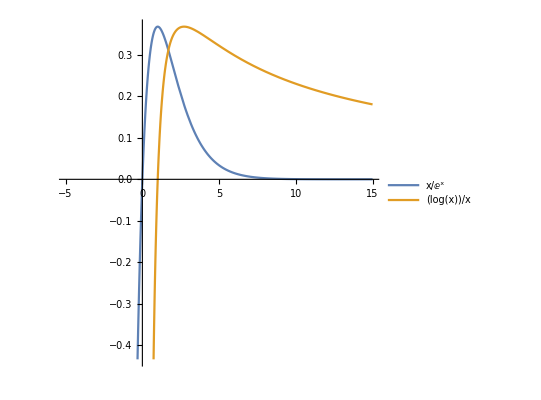

```mathematica
Plot[{x/ⅇ^x,Log[x]/x},{x,-5,15},AspectRatio->1,PlotLegends->"Expressions"]
```

```mathematica
ClearAll@f;
f[x_]:=Log[x]/x
Manipulate[Refresh[functions=Table[D[f[x],{x,n}],{n,0,nMax,1}];
orders=Table[D[f[x],{x,n}]//Inactivate//TraditionalForm//ToString,{n,0,nMax,1}];
labels=MapThread[#1<>" = "<>ToString[#2,TraditionalForm]&,{orders,functions}];];
Plot[functions,{x,0,3},PlotLabels->labels,ImageSize->700,AspectRatio->1,PlotLabel->Row[{"f(x) = ",f[x]}]],{{nMax,1,"Order"},1,10,1,PopupMenu}] (* AspectRatio->Automatic 横纵坐标相等  AspectRatio->1  横纵坐标不相等*)
```

```mathematica
ClearAll[Evaluate[Context[]<>"*"]]
eqns={x^2/a^2+y^2/b^2==1,y==k x+m};
polyex=Apply[Subtract,eqns,{1}];
polys=Numerator[Together[Apply[Subtract,eqns,{1}]]];
xpoly=Collect[Resultant[polys[[1]],polys[[2]],y],x]
discx=Factor[Discriminant[xpoly,x]]   (*discriminant*)
frist=Solve[eqns,{x,y}]//FullSimplify;
{{x1,y1},{x2,y2}}={x,y}/.frist;
second={x1+x2,x1 x2,y1+y2,y1 y2,y1 y2/(x1 x2)}//FullSimplify
thrid={x1 x2+y1 y2,x1 y2+x2 y1}//FullSimplify
slope=-CoefficientList[polyex[[2]],x][[2]];    (*k*)
intercept=-CoefficientList[CoefficientList[polyex[[2]],y][[1]],x][[1]] ;  (*m*)
Chordlength=FullSimplify[Sqrt[1+slope^2] Sqrt[(x1+x2)^2-4 x1 x2]]    (*AbsAB*)
area=1/2 Chordlength Sqrt[intercept^2]/Sqrt[slope^2+1]//FullSimplify
```

-a^2 b^2+a^2 m^2+2 a^2 k m x+(b^2+a^2 k^2) x^2

4 a^2 b^2 (b^2+a^2 k^2-m^2)

{-(2 a^2 k m)/(b^2+a^2 k^2),(a^2 (-b^2+m^2))/(b^2+a^2 k^2),(2 b^2 m)/(b^2+a^2 k^2),(b^2 (-a^2 k^2+m^2))/(b^2+a^2 k^2),(b^2 (a^2 k^2-m^2))/(a^2 (b^2-m^2))}

{(-a^2 b^2 (1+k^2)+(a^2+b^2) m^2)/(b^2+a^2 k^2),-(2 a^2 b^2 k)/(b^2+a^2 k^2)}

2 √(1+k^2) √((a^2 b^2 (b^2+a^2 k^2-m^2))/((b^2+a^2 k^2)^2))

√(m^2) √((a^2 b^2 (b^2+a^2 k^2-m^2))/((b^2+a^2 k^2)^2))

```mathematica
ClearAll[Evaluate[Context[]<>"*"]]
eqns={x^2/8+y^2/6==1,y==k x+m};
polyex=Apply[Subtract,eqns,{1}];
polys=Numerator[Together[Apply[Subtract,eqns,{1}]]];
xpoly=Collect[Resultant[polys[[1]],polys[[2]],y],x]
discx=Factor[Discriminant[xpoly,x]]   (*discriminant*)
frist=Solve[eqns,{x,y}]//FullSimplify;
{{x1,y1},{x2,y2}}={x,y}/.frist;
second={x1+x2,x1 x2,y1+y2,y1 y2,y1 y2/(x1 x2)}//FullSimplify
thrid={x1 x2+y1 y2,x1 y2+x2 y1}//FullSimplify
slope=-CoefficientList[polyex[[2]],x][[2]];    (*k*)
intercept=-CoefficientList[CoefficientList[polyex[[2]],y][[1]],x][[1]] ;  (*m*)
Chordlength=FullSimplify[Sqrt[1+slope^2] Sqrt[(x1+x2)^2-4 x1 x2]]    (*AbsAB*)
area=1/2 Chordlength Sqrt[intercept^2]/Sqrt[slope^2+1]//FullSimplify
```

-24+4 m^2+8 k m x+(3+4 k^2) x^2

48 (6+8 k^2-m^2)

{-(8 k m)/(3+4 k^2),(4 (-6+m^2))/(3+4 k^2),(6 m)/(3+4 k^2),(3 (-8 k^2+m^2))/(3+4 k^2),(3 (-8 k^2+m^2))/(4 (-6+m^2))}

{(-24 (1+k^2)+7 m^2)/(3+4 k^2),-(48 k)/(3+4 k^2)}

4 √3 √(1+k^2) √((6+8 k^2-m^2)/((3+4 k^2)^2))

2 √3 √(m^2) √((6+8 k^2-m^2)/((3+4 k^2)^2))

```mathematica
(3 (-8 k^2+m^2))/(4 (-6+m^2))+3/4==0//FullSimplify
```

(-3+4 k^2)/(-6+m^2)==1

```mathematica
(-3+4 k^2)/(-6+m^2)==1&&2 √3 √(m^2) √((6+8 k^2-m^2)/((3+4 k^2)^2))//FullSimplify
```

(-3+4 k^2)/(-6+m^2)==1&&2 √3 √(m^2) √((6+8 k^2-m^2)/((3+4 k^2)^2))

```mathematica
Sqrt[intercept^2]/Sqrt[slope^2+1]
```

(√(m^2))/(√(1+k^2))

```mathematica
2 √3 √(m^2) √((6+8 k^2-m^2)/((3+4 k^2)^2))/.m^2->4k^2+3//Simplify
```

2 √3 √(1/(3+4 k^2)) √(3+4 k^2)

```mathematica
Solve[(-3+4 k^2)/(-6+m^2)==1/.m^2->m2,m2]/.m2 ->m^2 
2 √3 √(m^2) √((6+8 k^2-m^2)/((3+4 k^2)^2))/.%//Expand
```

{{m^2→3+4 k^2}}

{2 √3 √(1/(3+4 k^2)) √(3+4 k^2)}

```mathematica
Solve[(-3+4 k^2)/(-6+m^2)==1/. m^2]
```

```mathematica
ClearAll[Evaluate[Context[]<>"*"]]
eqns={x^2/a^2+y^2/b^2==1,y==k( x-x0)+y0};
polyex=Apply[Subtract,eqns,{1}];
polys=Numerator[Together[Apply[Subtract,eqns,{1}]]];
xpoly=Collect[Resultant[polys[[1]],polys[[2]],y],x]
discx=Factor[Discriminant[xpoly,x]]   (*discriminant*)
frist=Solve[eqns,{x,y}]//FullSimplify;
{{x1,y1},{x2,y2}}={x,y}/.frist;
second={x1+x2,x1 x2,y1+y2,y1 y2,y1 y2/(x1 x2)}//FullSimplify
thrid={x1 x2+y1 y2,x1 y2+x2 y1}//FullSimplify
slope=-CoefficientList[polyex[[2]],x][[2]];    (*k*)
intercept=-CoefficientList[CoefficientList[polyex[[2]],y][[1]],x][[1]] ;  (*m*)
Chordlength=FullSimplify[Sqrt[1+slope^2] Sqrt[(x1+x2)^2-4 x1 x2]]    (*AbsAB*)
area=1/2 Chordlength Sqrt[intercept^2]/Sqrt[slope^2+1]//FullSimplify
```

-a^2 b^2+(b^2+a^2 k^2) x^2+a^2 k^2 x0^2-2 a^2 k x0 y0+a^2 y0^2+x (-2 a^2 k^2 x0+2 a^2 k y0)

4 a^2 b^2 (b^2+a^2 k^2-k^2 x0^2+2 k x0 y0-y0^2)

{(2 a^2 k (k x0-y0))/(b^2+a^2 k^2),-(a^2 (b^2-(-k x0+y0)^2))/(b^2+a^2 k^2),(2 b^2 (-k x0+y0))/(b^2+a^2 k^2),-(b^2 (a^2 k^2-(-k x0+y0)^2))/(b^2+a^2 k^2),(b^2 (a^2 k^2-(-k x0+y0)^2))/(a^2 (b^2-(-k x0+y0)^2))}

{(b^2 (-k x0+y0)^2+a^2 (-b^2 (1+k^2)+(-k x0+y0)^2))/(b^2+a^2 k^2),-(2 a^2 b^2 k)/(b^2+a^2 k^2)}

2 √(1+k^2) √((a^2 b^2 (b^2+a^2 k^2-(-k x0+y0)^2))/((b^2+a^2 k^2)^2))

√((-k x0+y0)^2) √((a^2 b^2 (b^2+a^2 k^2-(-k x0+y0)^2))/((b^2+a^2 k^2)^2))

```mathematica
ClearAll[Evaluate[Context[]<>"*"]]
eqn={b^2+a^2 k^2-k^2 x0^2+2 k x0 y0-y0^2==0}
aa=Solve[eqn,{k}]//FullSimplify;
{k1,k2}={k}/.aa;
k1 k2//FullSimplify
```

{b^2+a^2 k^2-k^2 x0^2+2 k x0 y0-y0^2==0}

{(b^2-y0^2)/(a^2-x0^2)}

```mathematica
Solve[(-3+4 k^2)/(-6+m^2)==1/.m^2->m2,m2]/.m2 ->m^2 
2 √3 √(m^2) √((6+8 k^2-m^2)/((3+4 k^2)^2))/.%
```

{{m^2→3+4 k^2}}

{2 √3 √(1/(3+4 k^2)) √(3+4 k^2)}

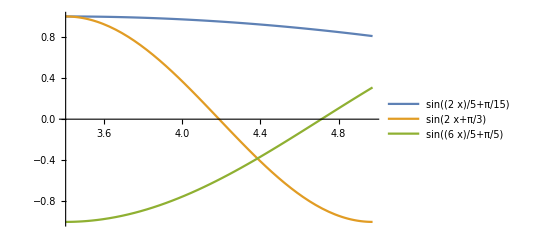

```mathematica
Plot[{Sin[2/5 x+π/15],Sin[2x+π/3],Sin[6/5 x+π/5]},{x,(13π)/12,(19π)/12},PlotLegends->"Expressions"]
```

```mathematica
Collect[-12+(3+4 k^2) x^2+4 k^2 x0^2-8 k x0 y0+4 y0^2+x (-8 k^2 x0+8 k y0),x]//FullSimplify
{%==0}
```

(3+4 k^2) x^2+8 k x (-k x0+y0)+4 (-3+(-k x0+y0)^2)

{(3+4 k^2) x^2+8 k x (-k x0+y0)+4 (-3+(-k x0+y0)^2)==0}